# Phase space Project “PHS”

Fateme Dashti - Arash T. Jamshidi

January 2023

### Step 0

In this project we trying to simulate trajectory of pendulum which is connected to a disk, and the disk it self has an angular momentum ω and analysis phase space of ω and the pendulum initial angel at t = 0 (θ_(t=0)).
we use Lagrangian mechanics and Euler-Lagrange equation to analysis this problem.

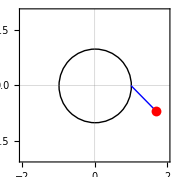

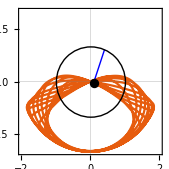
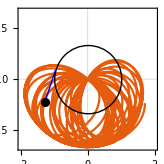

Piecewise[{{x[t]=, lSin[θ]+rCos[ϕ]}, {y[t]=, rSin[ϕ]-lCos[θ]}}]
ϕ=ωt
->Piecewise[{{x'[t]=, lθ' Cos[θ]-rωSin[ωt]}, {y'[t]=, rωCos[ωt]+lθ' Sin[θ]}}]
->T=1/2 m(x^(′^2)+y^(′^2))=1/2 m[l^2 θ^(′^2)+r^2 ω^2+2 rωlθ'+Sin[θ-ωt]]
U=mgy=mg[rSin[ϕ]-lCos[θ]]
L=T-U=1/2 m[l^2 θ^(′^2)+a^2 ω^2+2 rωlθ'+Sin[θ-ωt]]-mg[rSin[ϕ]-lCos[θ]]
(∂L)/(∂θ)-ⅆ/ⅆt(∂L)/(∂θ')=0
θ''[t]=-g/l Sin[θ[t]]+r ω^2/l Cos[θ[t]-ωt]

### Step 1

```mathematica
Quit
```

```mathematica
g:=9.8
l:=1(*Pendulum arm length*)
r:=1(*radius of disk*)
w:=6(*Angular momentum of disk*)
tmax:=50(*time range*)
(*{t=50,π/5,1}not*)
(*{t=50,π/10,3}Rot*)
```

```mathematica
solv=Flatten[NDSolve[{θ''[t]==-g/l*Sin[θ[t]]+r*w^2/l Cos[θ[t]-w*t],θ[0]==π/4,θ'[0]==0},{θ[t]},{t,0,tmax}]]
θ[t_]:=Evaluate[θ[t]/.solv]
```

{θ[t]→InterpolatingFunction[…][t]}

```mathematica
y1[t_]:=r*Sin[w*t]
x1[t_]:=r*Cos[w*t]
x2[t_]:=x1[t]+l*Sin[θ[t]]
y2[t_]:=y1[t]-l*Cos[θ[t]]
```

```mathematica
Manipulate[Show[ParametricPlot[{x2[t1],y2[t1]},{t1,0,t},Background->White,PlotTheme->"Scientific",PlotRange->{{-2,2},{-2,2}}],Graphics[{Thick,Blue,Line[{{x1[t],y1[t]},{x2[t],y2[t]}}]}],Graphics[{Circle[{0,0},r]}],Graphics[{PointSize[0.04],Black,Point[{x2[t],y2[t]}]}]],{t,10^-10,tmax}]
```

### Step 2

```mathematica
Quit
```

```mathematica
g:=9.8
l:=1(*Pendulum arm length*)
r:=1(*radius of disk*)
tmax:=25(*time range*)
ωstart:=-3
ωend:=3
ωstep:=0.1
θstart:=-π/4
θend:=π/4
θstep:=π/100
```

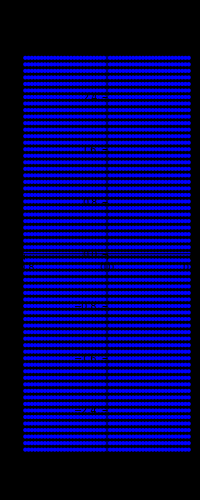

```mathematica
xy=Table[{θ0,ω},{θ0,θstart,θend,θstep},{ω,ωstart,ωend,ωstep}];


lenθ:=(θend-θstart)/θstep+1
lenω:=(ωend-ωstart)/ωstep+1


PHS:={}
Do[{
Do[{
data=xy[[i]][[j]]
,AppendTo[PHS,data]}
,{j,1,lenω}]}
,{i,1,lenθ}]


ListPlot[PHS,AspectRatio->Full,
PlotStyle->{Blue,PointSize[Small]},
Background->Black,
Axes->True,
PlotLabel->"Phase space",
PlotRange->All]
```

```mathematica
PHS;
```

```mathematica
Length[PHS]
```

3111

### Step 3

```mathematica
firstRdata:={}
Do[{
Clear[θ],
theta=PHS[[α]][[1]];

ω=PHS[[α]][[2]];

eqf1=θ[t]/.Flatten[NDSolve[{ θ''[t]+g/l*Sin[θ[t]]-r*ω^2/l Cos[θ[t]-ω*t]==0,θ[0]==theta,θ'[0]==0},θ[t],{t,0,tmax}]];
Do[{
If[(eqf1/.t->t1)>π,{AppendTo[firstRdata,{theta,ω}],Break[]},Null]
},{t1,0,tmax}]

},{α,1,Length@PHS}]
```

```mathematica
Length[firstRdata]
```

483

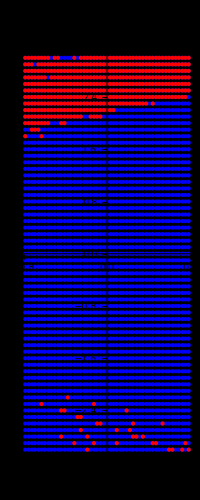

```mathematica
Show[ListPlot[PHS,AspectRatio->Full,
PlotStyle->{Blue,PointSize[Medium]},
Axes->True,
PlotLabel->"Phase space",
PlotRange->All],ListPlot[firstRdata,PlotStyle->{Red,PointSize[Medium]}],Background->Black]
```

```mathematica
secondRdata:={}
Do[{
Clear[θ],
theta=PHS[[α]][[1]];

ω=PHS[[α]][[2]];

eqf1=θ[t]/.Flatten[NDSolve[{ θ''[t]+g/l*Sin[θ[t]]-r*ω^2/l Cos[θ[t]-ω*t]==0,θ[0]==theta,θ'[0]==0},θ[t],{t,0,tmax}]];
Do[{
If[(eqf1/.t->t1)>3*π,{AppendTo[secondRdata,{theta,ω}],Break[]},Null]
},{t1,0,tmax}]

},{α,1,Length@PHS}]
```

```mathematica
Length[secondRdata];
```

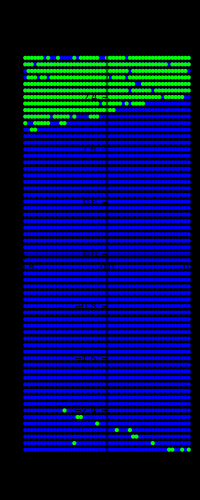

```mathematica
Show[ListPlot[PHS,AspectRatio->Full,
PlotStyle->{Blue,PointSize[Medium]},
Axes->True,
PlotLabel->"Phase space",
PlotRange->All],ListPlot[secondRdata,PlotStyle->{Green,PointSize[Medium]}],Background->Black]
```

```mathematica
thirdRdata:={}
Do[{
Clear[θ],
theta=PHS[[α]][[1]];

ω=PHS[[α]][[2]];

eqf1=θ[t]/.Flatten[NDSolve[{ θ''[t]+g/l*Sin[θ[t]]-r*ω^2/l Cos[θ[t]-ω*t]==0,θ[0]==theta,θ'[0]==0},θ[t],{t,0,tmax}]];
Do[{
If[(eqf1/.t->t1)>5*π,{AppendTo[thirdRdata,{theta,ω}],Break[]},Null]
},{t1,0,tmax}]

},{α,1,Length@PHS}]
```

```mathematica
Length[thirdRdata];
```

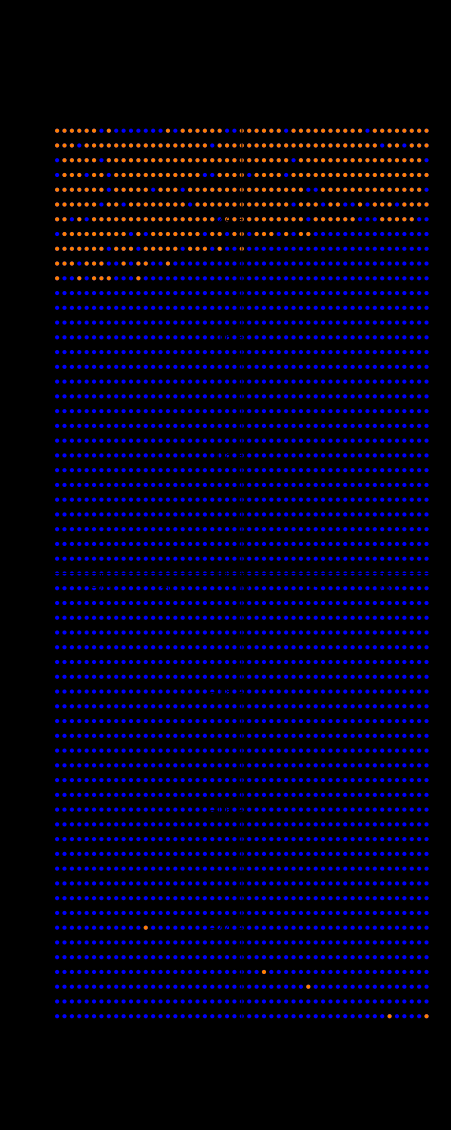

```mathematica
Show[ListPlot[PHS,AspectRatio->Full,
PlotStyle->{Blue,PointSize[Medium]},
Axes->True,
PlotLabel->"Phase space",
PlotRange->All],ListPlot[thirdRdata,PlotStyle->{Orange,PointSize[Medium]}],Background->Black]
```

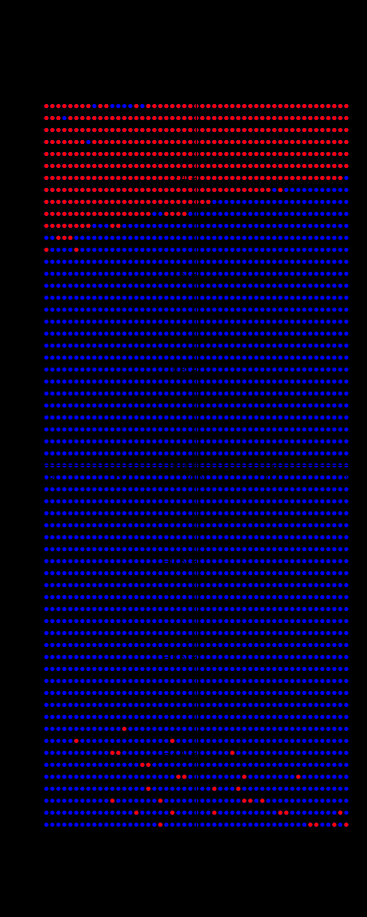
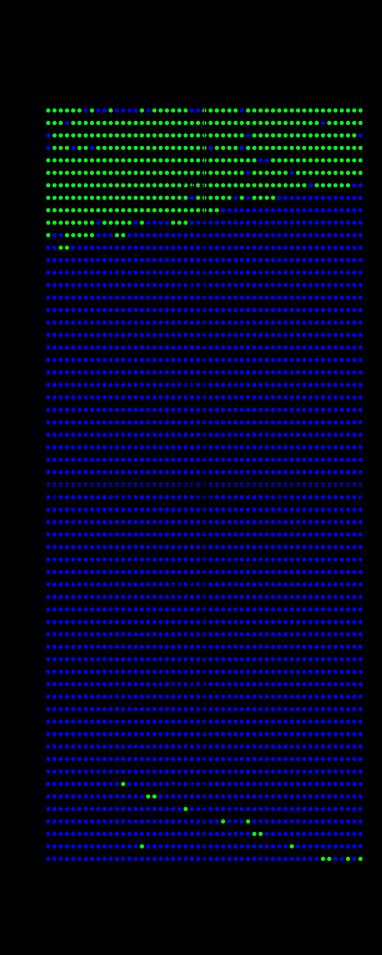
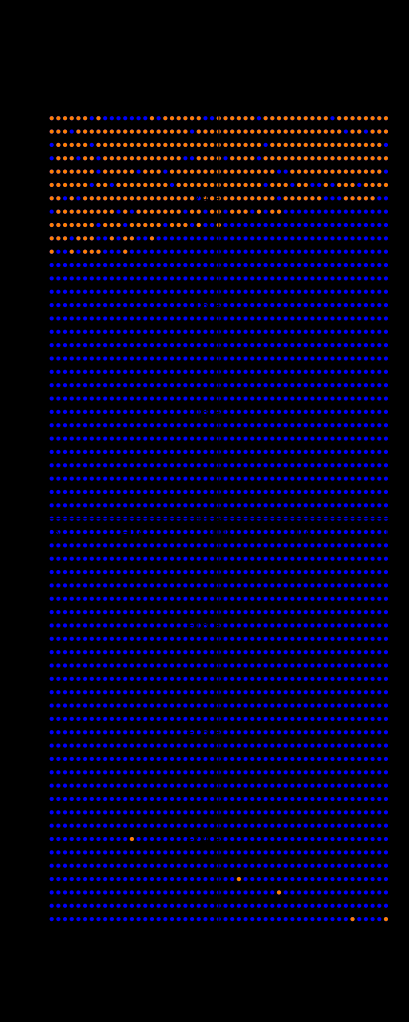

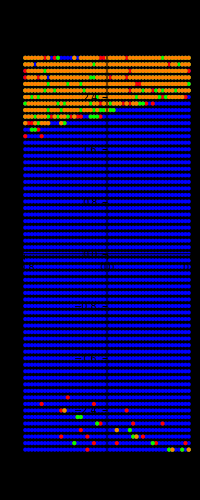

```mathematica
Show[
ListPlot[PHS,AspectRatio->Full,
PlotStyle->{Blue,PointSize[Medium]},
Axes->True,
PlotLabel->"Phase space",
PlotRange->All],
ListPlot[firstRdata,PlotStyle->{Red,PointSize[Medium]}],

ListPlot[secondRdata,PlotStyle->{Green,PointSize[Medium]}],

ListPlot[thirdRdata,PlotStyle->{Orange,PointSize[Medium]}]
,Background->Black]
```

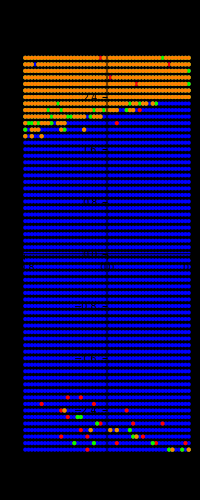

### Step 4

```mathematica
Quit
```

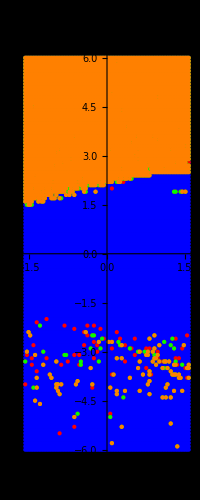

```mathematica
g:=9.8
l:=1(*Pendulum arm length*)
r:=1(*radius of disk*)
tmax:=50(*time range*)
ωstart:=-6
ωend:=6
ωstep:=0.1
θstart:=-π/2
θend:=π/2
θstep:=π/100

firstRdata:={}
secondRdata:={}
thirdRdata:={}

xy=Table[{θ0,ω},{θ0,θstart,θend,θstep},{ω,ωstart,ωend,ωstep}];

lenθ:=(θend-θstart)/θstep+1
lenω:=(ωend-ωstart)/ωstep+1

PHS:={}
Do[{
Do[{
data=xy[[i]][[j]]
,AppendTo[PHS,data]}
,{j,1,lenω}]}
,{i,1,lenθ}]

firstRdata:={}
Do[{
Clear[θ],
theta=PHS[[α]][[1]];

ω=PHS[[α]][[2]];

eqf1=θ[t]/.Flatten[NDSolve[{ θ''[t]+g/l*Sin[θ[t]]-r*ω^2/l Cos[θ[t]-ω*t]==0,θ[0]==theta,θ'[0]==0},θ[t],{t,0,tmax}]];
Do[{
If[(eqf1/.t->t1)>π,{AppendTo[firstRdata,{theta,ω}],Break[]},Null]
},{t1,0,tmax}]

},{α,1,Length@PHS}]

Do[{
Clear[θ],
theta=PHS[[α]][[1]];

ω=PHS[[α]][[2]];

eqf1=θ[t]/.Flatten[NDSolve[{ θ''[t]+g/l*Sin[θ[t]]-r*ω^2/l Cos[θ[t]-ω*t]==0,θ[0]==theta,θ'[0]==0},θ[t],{t,0,tmax}]];
Do[{
If[(eqf1/.t->t1)>3*π,{AppendTo[secondRdata,{theta,ω}],Break[]},Null]
},{t1,0,tmax}]

},{α,1,Length@PHS}]

Do[{
Clear[θ],
theta=PHS[[α]][[1]];

ω=PHS[[α]][[2]];

eqf1=θ[t]/.Flatten[NDSolve[{ θ''[t]+g/l*Sin[θ[t]]-r*ω^2/l Cos[θ[t]-ω*t]==0,θ[0]==theta,θ'[0]==0},θ[t],{t,0,tmax}]];
Do[{
If[(eqf1/.t->t1)>5*π,{AppendTo[thirdRdata,{theta,ω}],Break[]},Null]
},{t1,0,tmax}]

},{α,1,Length@PHS}]

Show[
ListPlot[PHS,AspectRatio->Full,
PlotStyle->{Blue,PointSize[Medium]},
Axes->True,
PlotLabel->"Phase space",
PlotRange->All],
ListPlot[firstRdata,PlotStyle->{Red,PointSize[Medium]}],

ListPlot[secondRdata,PlotStyle->{Green,PointSize[Medium]}],

ListPlot[thirdRdata,PlotStyle->{Orange,PointSize[Medium]}]
,Background->Black]
```

-Graphics-